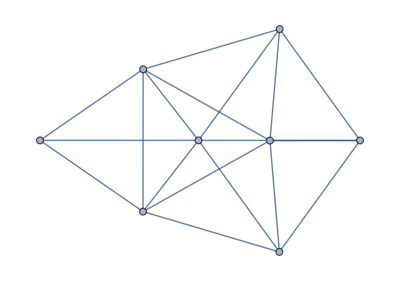

```mathematica
g10=ReadGrof[11]
```

```mathematica
ChromaticPolynomial[g10,4]
```

120

```mathematica
me10=MissingEdges2[g10]
```

{1<->4,2<->8,1<->5,1<->6,6<->8,4<->7}

```mathematica
FindFullFormula4[g10]
```

```mathematica
{v18x24x35x67,v14x28x35x67,;,v16x28x35x47,v168x24x35x7}
```

```mathematica
Table[e<->FindFullFormula4[EdgeAdd[g10,e]],{e,me10}]
```

{(1<->4)<->{v18x24x35x67,v168x2x35x47,v16x28x35x47,v168x24x35x7},2<->8<->{v18x24x35x67,v168x2x35x47,v168x24x35x7},(1<->5)<->{v18x24x35x67,v14x28x35x67,v168x2x35x47,v16x28x35x47,v168x24x35x7},(1<->6)<->{v18x24x35x67,v14x28x35x67},6<->8<->{v18x24x35x67,v14x28x35x67,v16x28x35x47},(4<->7)<->{v18x24x35x67,v14x28x35x67,v168x24x35x7}}

```mathematica
Table[ChromaticPolynomial[EdgeContract[EdgeAdd[g10,e],e],4],{e,me10}]
```

{24,48,0,72,48,48}

```mathematica
SetsEquals[s1_,s2_]:=Length[s1]==Length[s2]&&Length[Intersection[s1,s2]]==Length[s1]==Length[s2]
```

```mathematica
Table[e<->FindFullFormula4[EdgeContract[EdgeAdd[g10,e],e]],{e,me10}]
```

{(1<->4)<->{v1x28x35x67},2<->8<->{v14x2x35x67,v16x2x35x47},(1<->5)<->{},(1<->6)<->{v18x2x35x47,v1x28x35x47,v18x24x35x7},6<->8<->{v16x2x35x47,v16x24x35x7},(4<->7)<->{v168x2x35x4,v16x28x35x4}}

```mathematica
Table[With[{g=ReadGrof[k]},
With[{full=FindFullFormula4[g]},
{k,(ChromaticPolynomial[g,4]/24)}<->Table[SetsEquals[full,FindFullFormula4[EdgeAdd[g,e]]],{e,MissingEdges2[g]}]
]
],
{k,Select[Range[50],ChromaticPolynomial[ReadGrof[#],4]!=24&]}]//TableForm
```

{4,4}<->{False}
{6,4}<->{False,False,False}
{7,5}<->{False,False,False}
{11,5}<->{False,False,True,False,False,False}
{14,4}<->{True,True,False,False,False}
{15,4}<->{False,False,False,False,False,False}
{18,3}<->{False,False,False,False,False,False}
{19,4}<->{False,False,False,False,False,False}
{20,4}<->{False,False,False,False,False,False}
{21,12}<->{False,False,False,False,False}
{25,4}<->{True,False,True,True,False,False,False,False,False}
{26,5}<->{True,True,True,True,False,False,False,False}
{30,4}<->{True,False,True,False,False,True,True,True}
{31,5}<->{False,False,False,True,True,False,False,False,False}
{35,4}<->{False,False,True,True,False,False,False,False,False}
{36,3}<->{False,False,True,False,False,False,False,False,False}
{37,12}<->{False,False,False,False,False,False,False,False}
{38,3}<->{True,False,False,False,False,False,False,False,False}
{39,5}<->{False,True,False,True,False,False,False,True}
{40,9}<->{False,False,False,False,True,False,True,False}
{41,6}<->{True,True,False,False,False,False,False,True,False}
{42,5}<->{False,False,False,True,True,False,False,False,False}
{43,5}<->{False,False,False,True,True,False,False,False,False}
{44,5}<->{False,False,False,True,True,False,False,False,False}
{45,5}<->{False,False,False,True,True,False,False,False,False}
{46,2}<->{True,True,True,True,True,True,False,False,False}
{49,4}<->{False,False,False,False,False,False,False,True,True}

```mathematica
.
```

```mathematica
Table[With[{g=ReadGrof[k]},
With[{full=FindFullFormula4[g]},
{k,(ChromaticPolynomial[g,4]/24)}<->Fold[Or,Table[SetsEquals[full,FindFullFormula4[EdgeAdd[g,e]]],{e,MissingEdges2[g]}]]
]
],
{k,Range[80]}]//TableForm
```

{1,1}<->Fold[Or,{}]
{2,1}<->Fold[Or,{}]
{3,1}<->True
{4,4}<->False
{5,1}<->True
{6,4}<->False
{7,5}<->False
{8,1}<->True
{9,1}<->True
{10,1}<->True
{11,5}<->True
{12,1}<->True
{13,1}<->True
{14,4}<->True
{15,4}<->False
{16,1}<->True
{17,1}<->True
{18,3}<->False
{19,4}<->False
{20,4}<->False
{21,12}<->False
{22,1}<->True
{23,1}<->True
{24,1}<->True
{25,4}<->True
{26,5}<->True
{27,1}<->True
{28,1}<->True
{29,1}<->True
{30,4}<->True
{31,5}<->True
{32,1}<->True
{33,1}<->True
{34,1}<->True
{35,4}<->True
{36,3}<->True
{37,12}<->False
{38,3}<->True
{39,5}<->True
{40,9}<->True
{41,6}<->True
{42,5}<->True
{43,5}<->True
{44,5}<->True
{45,5}<->True
{46,2}<->True
{47,1}<->True
{48,1}<->True
{49,4}<->True
{50,1}<->True
{51,1}<->True
{52,1}<->True
{53,1}<->True
{54,1}<->True
{55,1}<->True
{56,4}<->True
{57,4}<->True
{58,1}<->True
{59,1}<->True
{60,1}<->True
{61,1}<->True
{62,16}<->False
{63,4}<->True
{64,4}<->True
{65,4}<->False
{66,4}<->False
{67,4}<->False
{68,1}<->True
{69,1}<->True
{70,1}<->True
{71,1}<->True
{72,21}<->False
{73,1}<->True
{74,1}<->True
{75,1}<->True
{76,5}<->True
{77,1}<->True
{78,4}<->True
{79,4}<->True
{80,12}<->False

```mathematica
Monitor[Flatten[Table[With[{g=ReadGrof[k]},
With[{full=ChromaticPolynomial[g,4]/24},
Table[{ChromaticPolynomial[EdgeAdd[g,e],4]/24,full},{e,MissingEdges2[g]}]
]
],
{k,3,10000}],1]//DeleteDuplicates,k]//ListPlot
```

$Aborted